```mathematica
ClearAll["Global`*"]

(*The warp factor in conformal coordinates, Reff eqn(10)*)
Zp = 1/(w Csc[k w z]); (*0 < z ≤ π/(2 k w)*)

M5sq = -3 k^2; (*Refer eqn(13)*)

Deqn = D[1/Zp^3 D[X[z],z],z] - M5sq/Zp^5 X[z] == 0; (*scalar field EOM*)

DSolve[Deqn,X[z],z]
```

{{X[z]→C[2] Sin[k w z]^3+C[1] (-Csc[(k w z)/2]^2/(8 k w)-Log[Cos[(k w z)/2]]/(2 k w)+Log[Sin[(k w z)/2]]/(2 k w)+Sec[(k w z)/2]^2/(8 k w)) Sin[k w z]^3}}

```mathematica
X[z_] = (s Sin[k w z]^3/(k w)^3+-mq   (-Csc[(k w z)/2]^2/(4 k w)-Log[Cos[(k w z)/2]]/(k w)+Log[Sin[(k w z)/2]]/(k w)+Sec[(k w z)/2]^2/(4 k w)) Sin[k w z]^3)k^(3/2); (* scalar field solution*)
```

```mathematica
zms = Import[NotebookDirectory[]<>"zms.mx"];
wvals = Import[NotebookDirectory[]<>"wvals.mx"];
```

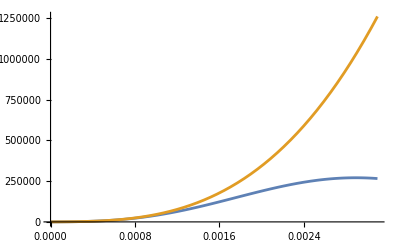

```mathematica
a=-1;
Block[{k=10000,w=wvals[[a]],mq=345/100,zm = zms[[a]],s= 1/zm^3},
Plot[{X[z],k^(3/2)(mq z+ s z^3)},{z,0,1/323},PlotRange->All] (*Comparision of the scalar field solution with (Blue) and without (Orange) ω *)
]
```